## Find the middle-cutting longitude

```mathematica
(*Order of magnitude for number of random points*)
n=10000;
```

```mathematica
points=RandomGeoPosition[Entity["GeographicRegion", "World"],n];
GeoGraphics[{PointSize@.0025,Point@points},GeoProjection->"Mollweide"]
```

-Graphics-

```mathematica
GeoArea@Entity["GeographicRegion", "World"]
```

1.46865×10^8 km^2

```mathematica
(*Get the list of latitudes and longitudes of generated points,
and sort the points by their longitudes*)
info=With[{latlong=points[[1]]},SortBy[
Which[Last@#>180,#-{0,360},
Last@#<-180,#+{0,360},
True,#]&/@latlong,
#[[2]]&]];
```

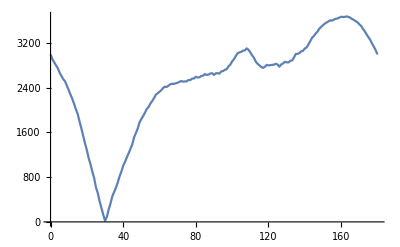

```mathematica
(*Get the east-west-difference of the number of points for each longitude*)
ewd[x_]:=With[{t=CountsBy[info,#[[2]]>x-180&&#[[2]]<=x&]},n-2First@t]
ListPlot[Table[Abs@ewd[x],{x,0,180}],Joined->True,DataRange->{0,180}]
```

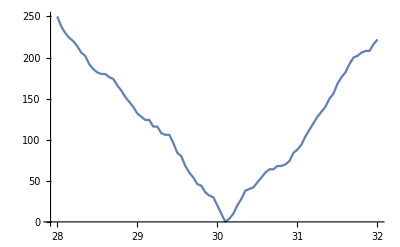

```mathematica
ListPlot[Table[Abs@ewd[x],{x,28,32,.05}],Joined->True,DataRange->{28,32}]
```

### and the middle-cutting latitude

```mathematica
lat=With[{latlong=points[[1]]},SortBy[latlong,#[[1]]&]];
```

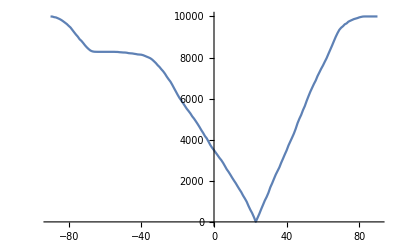

```mathematica
(*Get the north-south-difference of the number of points for each latitude*)
nsd[x_]:=With[{t=CountsBy[lat,#[[1]]>x&]},n-2First@t]
ListPlot[Table[Abs@nsd[x],{x,-90,90}],Joined->True,DataRange->{-90,90}]
```

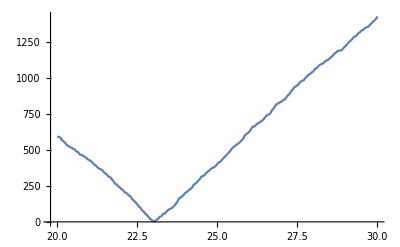

```mathematica
ListPlot[Table[Abs@nsd[x],{x,20,30,.05}],Joined->True,DataRange->{20,30}]
```